# Blatt 6

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],PrintPrecision->Round[MachinePrecision]]
```

## Import Data

```mathematica
rawData={155,184,5,135,134,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,130,8,20,216,7}
```

{155,184,5,135,134,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,130,8,20,216,7}

```mathematica
(*rawData={155,182,5,135,128,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,136,8,20,214,7}*) (*lisa data*)
```

```mathematica
(*rawData={155,184,5,135,131,4,120,99,4,100,49,1,90,53,3,75,55,1,65,70,4,55,81,9,40,133,8,20,216,7}*)
```

```mathematica
data=Partition[rawData,3]
```

{{155,184,5},{135,134,4},{120,99,4},{100,49,1},{90,53,3},{75,55,1},{65,70,4},{55,81,9},{40,130,8},{20,216,7}}

```mathematica
data//TeXForm//CopyToClipboard
```

## Processed Data

```mathematica
processedData={#[[1]],#[[2]]-2#[[3]],N@Sqrt[#[[2]]+4 #[[3]]]}&/@data
```

{{155,174,14.2829},{135,126,12.2474},{120,91,10.7238},{100,47,7.28011},{90,47,8.06226},{75,53,7.68115},{65,62,9.27362},{55,63,10.8167},{40,114,12.7279},{20,202,15.6205}}

```mathematica
veryProcessedData={#[[1]], N@Cos[#[[1]] Degree],#[[2]],#[[3]]}&/@processedData
```

{{155,-0.906308,174,14.2829},{135,-0.707107,126,12.2474},{120,-0.5,91,10.7238},{100,-0.173648,47,7.28011},{90,0.,47,8.06226},{75,0.258819,53,7.68115},{65,0.422618,62,9.27362},{55,0.573576,63,10.8167},{40,0.766044,114,12.7279},{20,0.939693,202,15.6205}}

```mathematica
veryProcessedData//TeXForm//CopyToClipboard
```

## Legendre Fitting

```mathematica
LegendreP[0,x]
LegendreP[1,x]
LegendreP[2,x]
```

1

x

1/2 (-1+3 x^2)

```mathematica
f1[x_]:=1
f2[x_]:= x
f3[x_]:=1/2 (-1+3 x^2)
```

```mathematica
xdata=N@Cos[# Degree]&/@processedData[[All,1]]
ydata=processedData[[All,2]]
yerror=processedData[[All,3]]
```

{-0.906308,-0.707107,-0.5,-0.173648,0.,0.258819,0.422618,0.573576,0.766044,0.939693}

{174,126,91,47,47,53,62,63,114,202}

{14.2829,12.2474,10.7238,7.28011,8.06226,7.68115,9.27362,10.8167,12.7279,15.6205}

```mathematica
flst={f1,f2,f3}
```

{f1,f2,f3}

```mathematica
MatrixForm[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

(0.101912 | 0.00600222 | -0.015904
0.00600222 | 0.023368 | -0.000349098
-0.015904 | -0.000349098 | 0.0179389)

```mathematica
Δ=Det[Table[∑_(k=1)^Length[xdata] (flst⟦i⟧[xdata⟦k⟧] flst⟦j⟧[xdata⟦k⟧])/yerror⟦k⟧^2,{i,1,3},{j,1,3}]]
```

0.0000362185

```mathematica
sumf1f1=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f2=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf1f3=∑_(k=1)^Length[xdata] (f1[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f2=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf2f3=∑_(k=1)^Length[xdata] (f2[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumf3f3=∑_(k=1)^Length[xdata] (f3[xdata⟦k⟧] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf1=∑_(k=1)^Length[xdata] (ydata[[k]] f1[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf2=∑_(k=1)^Length[xdata] (ydata[[k]] f2[xdata⟦k⟧])/yerror⟦k⟧^2;
sumyf3=∑_(k=1)^Length[xdata] (ydata[[k]] f3[xdata⟦k⟧])/yerror⟦k⟧^2;
```

```mathematica
Δ=Det[({{sumf1f1, sumf1f2, sumf1f3}, {sumf1f2, sumf2f2, sumf2f3}, {sumf1f3, sumf2f3, sumf3f3}})]
```

0.0000362185

```mathematica
a1=(1/Δ) Det[({{sumyf1, sumf1f2, sumf1f3}, {sumyf2, sumf2f2, sumf2f3}, {sumyf3, sumf2f3, sumf3f3}})]
a2=(1/Δ)Det[({{sumf1f1, sumyf1, sumf1f3}, {sumf1f2, sumyf2, sumf2f3}, {sumf1f3, sumyf3, sumf3f3}})]
a3=(1/Δ)Det[({{sumf1f1, sumf1f2, sumyf1}, {sumf1f2, sumf2f2, sumyf2}, {sumf1f3, sumf2f3, sumyf3}})]
```

93.3558

-11.8761

104.34

```mathematica
Sqrt[Sum[((1/Δ) Det[({{f1[xdata[[i]]]/yerror[[i]]^2+2sumyf1, sumf1f2, sumf1f3}, {f2[xdata[[i]]]/yerror[[i]]^2+2sumyf2, sumf2f2, sumf2f3}, {f2[xdata[[i]]]/yerror[[i]]^2+2sumyf3, sumf2f3, sumf3f3}})])^2 yerror[[i]]^2,{i,1,Length[yerror]}]]
```

6617.85

```mathematica
theory[x_]:=a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+ a3 f3[Cos[x Degree]]
```

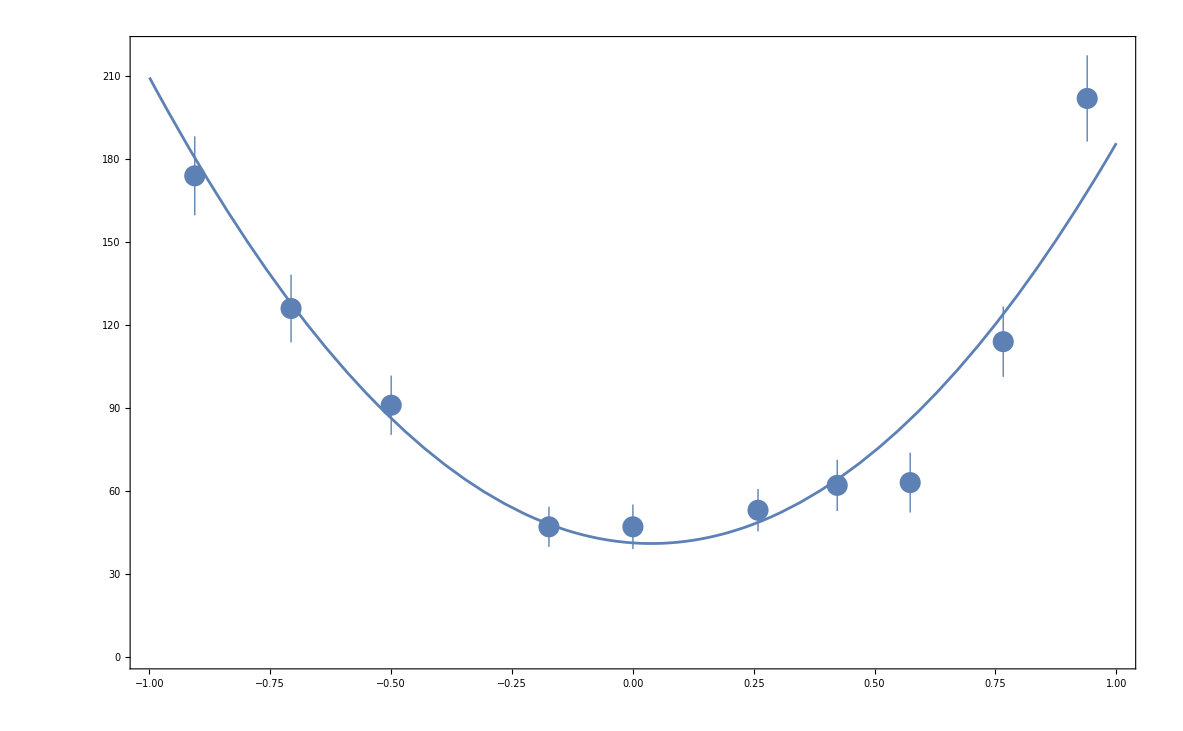

```mathematica
Show[Plot[a1+a2 x+a3(-1+3 x^2)/2,{x,-1,1},PlotRange->{{-2,2},All}],ListPlot[{Cos[#[[1]]Degree],Around[#[[2]],#[[3]]]}&/@processedData],Frame->True,PlotRange->{{-1,1},{0,220}},Axes->False]
```

```mathematica
cross=Graphics[{Line[{{-1,-1},{1,1}}],Line[{{1,-1},{-1,1}}]},ImageSize->11,ImagePadding->1.5]
```

-Graphics-

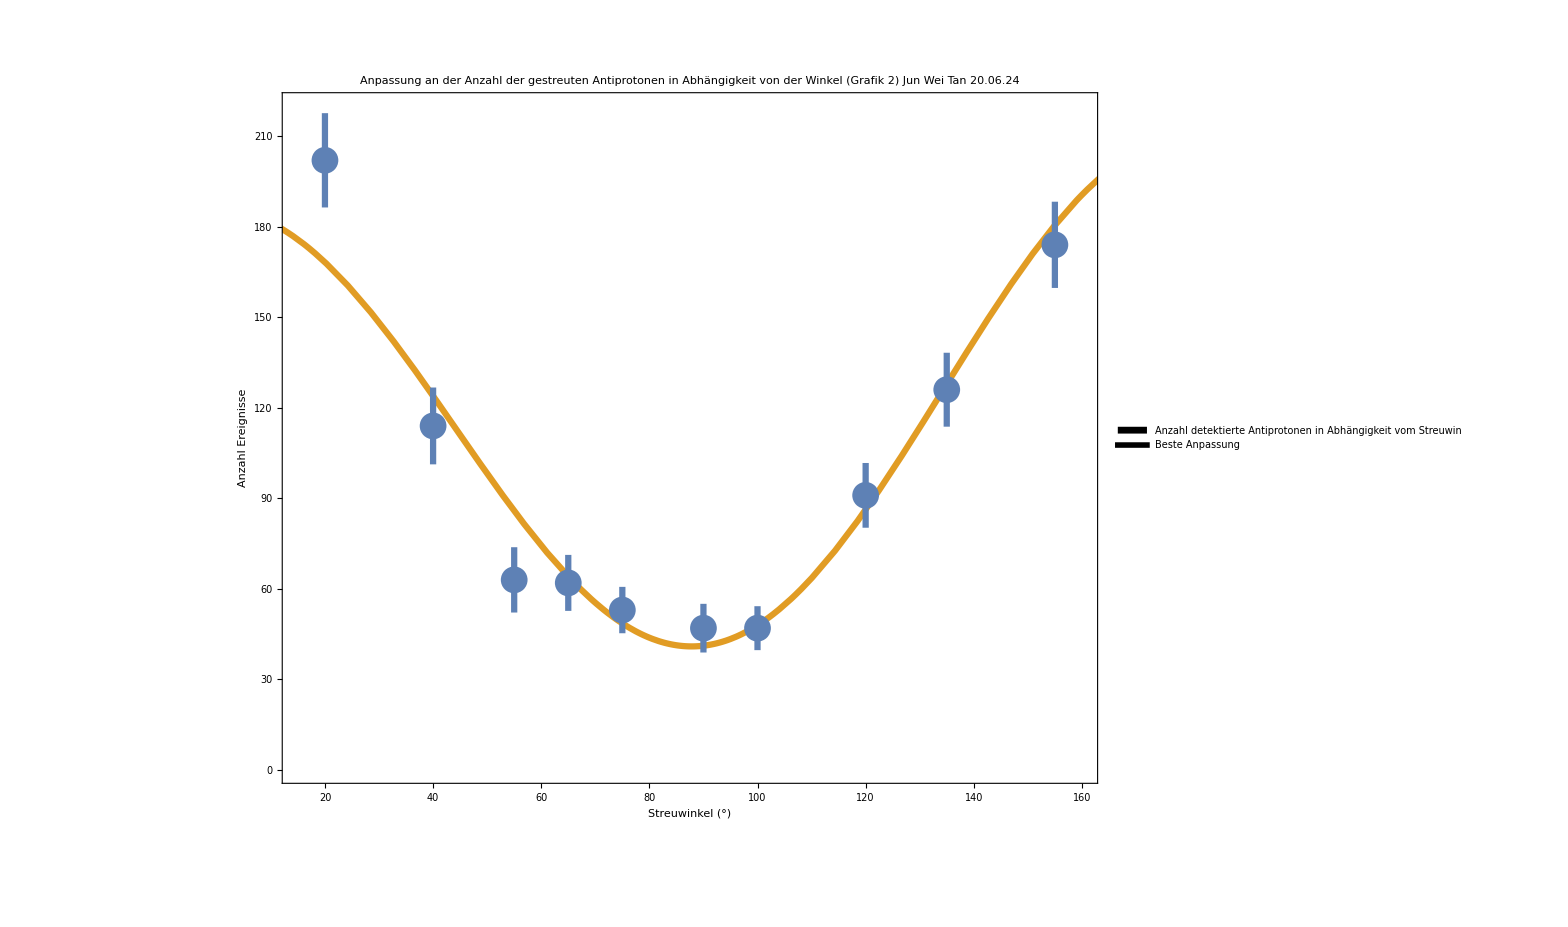

```mathematica
plt1=Legended[Show[ Plot[a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+a3 f3[Cos[x Degree]],{x,0,200},PlotStyle->Directive[ColorData[97,2],Thickness[0.003]]],ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData,PlotStyle->Thickness[0.003]],Frame->True,PlotRange->{{15,160},{0,220}},Axes->False,ImageSize->1500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[40,Black,Opacity[1],FontOpacity[1]],LabelStyle->Directive[Black,40,NumberPoint->","],FrameLabel->{"Streuwinkel (°)","Anzahl Ereignisse"},PlotLabel->"Anpassung an der Anzahl der gestreuten\n Antiprotonen in Abhängigkeit von der Winkel (Grafik 2)\n Jun Wei Tan 20.06.24"],Placed[SwatchLegend[{ColorData[97,1],ColorData[97,2]},{TextCell["Anzahl detektierte Antiprotonen\nin Abhängigkeit vom Streuwinkel mit Fehler",30],TextCell["Beste Anpassung",30]},LegendMarkers->{Graphics[{Disk[]},AspectRatio->1],Graphics[{Thickness[0.5],Line[{{0,0},{1,0}}]}]},LegendMarkerSize->20,Alignment->Center],{Scaled[0.30],Scaled[0.85]}]]
```

```mathematica
Export[NotebookDirectory[]<>"plt1.pdf",plt1,Background->None];
```

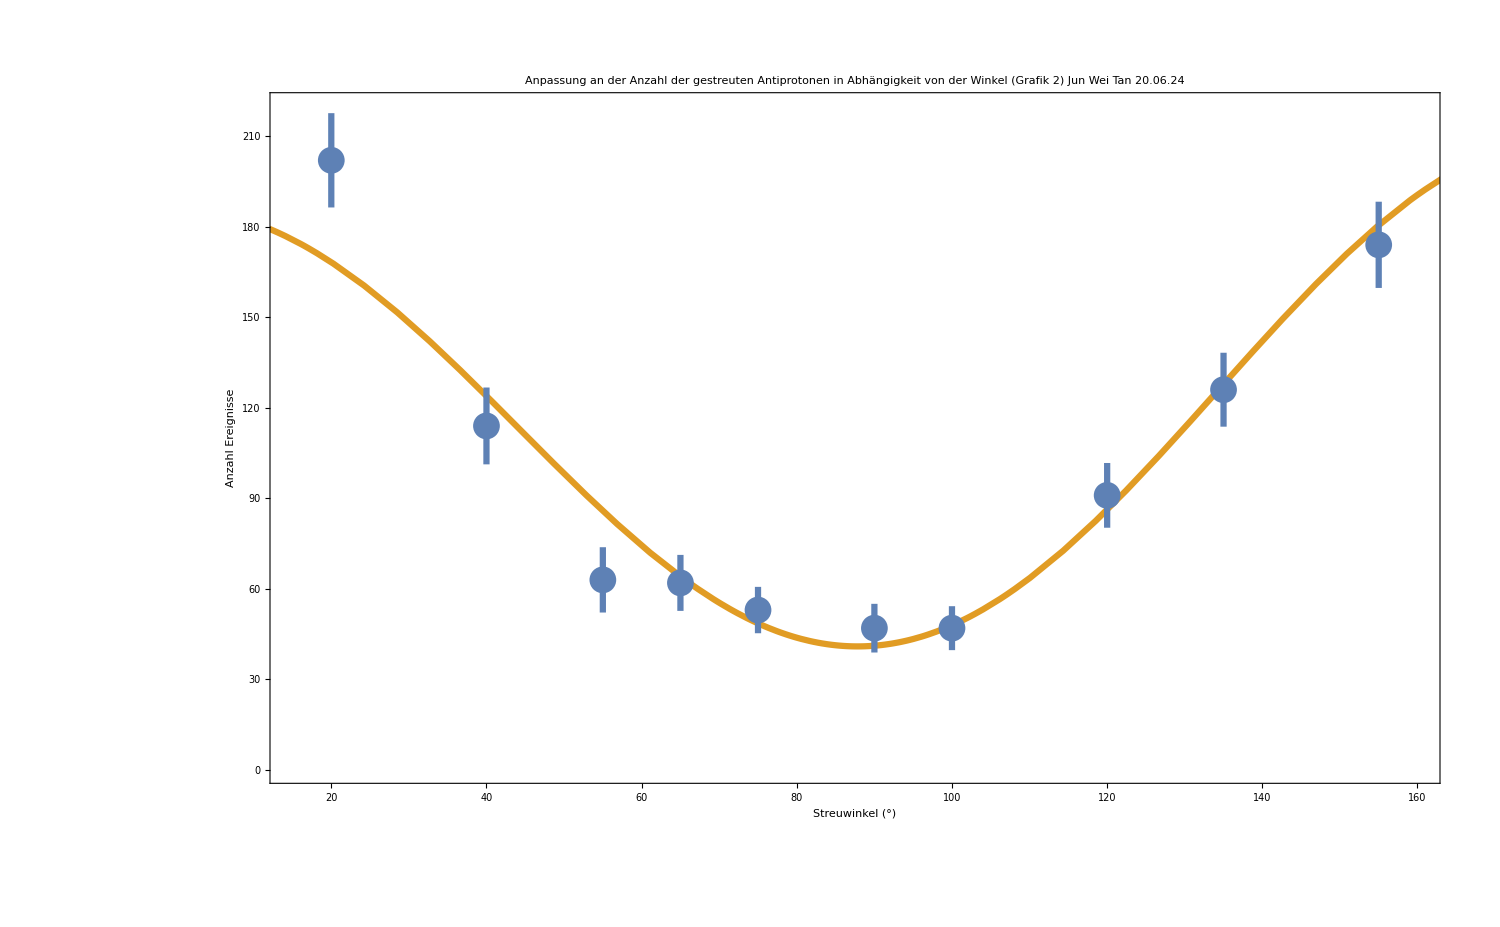

```mathematica
plt3=Show[ Plot[a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+a3 f3[Cos[x Degree]],{x,0,200},PlotStyle->Directive[ColorData[97,2],Thickness[0.003]]],ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData,PlotStyle->Thickness[0.003]],Frame->True,PlotRange->{{15,160},{0,220}},Axes->False,ImageSize->1500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[40,Black,Opacity[1],FontOpacity[1]],LabelStyle->Directive[Black,40,NumberPoint->","],FrameLabel->{"Streuwinkel (°)","Anzahl Ereignisse"},PlotLabel->"Anpassung an der Anzahl der gestreuten\n Antiprotonen in Abhängigkeit von der Winkel (Grafik 2)\n Jun Wei Tan 20.06.24"]
```

```mathematica
Export[NotebookDirectory[]<>"plt3.pdf",plt3,Background->None];
```

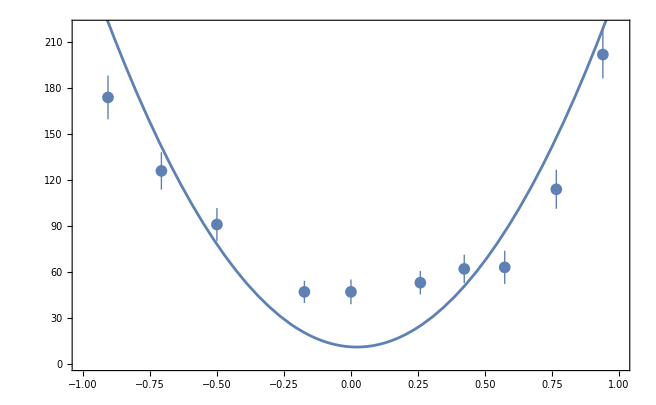

```mathematica
Show[ListPlot[{Cos[#[[1]]Degree],Around[#[[2]],#[[3]]]}&/@processedData], Plot[93.3-10.6 x+164.4(-1+3 x^2)/2,{x,-1,1}],Frame->True,PlotRange->{{-1,1},{0,220}},Axes->False]
```

```mathematica
FindFit[Transpose[{xdata, ydata}], a1f f1[x]+ a2f f2[x]+a3f f3[x],{a1f,a2f,a3f},x]
```

{a1f→93.2123,a2f→-7.68994,a3f→111.006}

```mathematica
mathematicafit=NonlinearModelFit[Transpose[{xdata, ydata}], a1f f1[x]+ a2f f2[x]+a3f f3[x],{a1f,a2f,a3f},x,Weights->1/yerror^2]
```

FittedModel[…]

```mathematica
mathematicafit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a1f | 93.3558 | 4.28273 | 21.7982 | 1.07911×10^-7
a2f | -11.8761 | 8.30328 | -1.43029 | 0.195716
a3f | 104.34 | 10.1318 | 10.2982 | 0.000017621

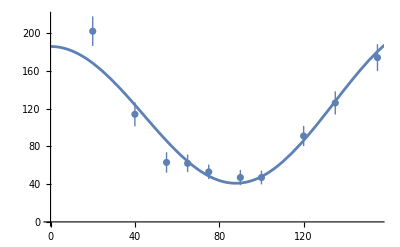

```mathematica
Show[ListPlot[{#[[1]],Around[#[[2]],#[[3]]]}&/@processedData], Plot[a1 f1[Cos[x Degree]]+a2 f2[Cos[x Degree]]+a3 f3[Cos[x Degree]],{x,0,200}]]
```

## Errors

```mathematica
({{f1[xdata⟦1⟧]/yerror⟦1⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦1⟧]/yerror⟦1⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦1⟧]/yerror⟦1⟧^2+2sumyf3, sumf2f3, sumf3f3}})//MatrixForm
```

(15.5717 | 0.00600222 | -0.015904
0.488352 | 0.023368 | -0.000349098
0.785893 | -0.000349098 | 0.0179389)

```mathematica
Table[Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf2f3, sumf3f3}})],{k,1,Length[xdata]}]
```

{0.00676625,0.00676631,0.00676611,0.00676749,0.00676603,0.00676657,0.00676579,0.00676548,0.00676539,0.00676499}

```mathematica
(1/Δ) Sqrt[Sum[(Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf2f3, sumf3f3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
(1/Δ) Sqrt[Sum[(Det[({{sumf1f1, f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1, sumf1f3}, {sumf1f2, f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2, sumf2f3}, {sumf1f3, f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3, sumf3f3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
(1/Δ) Sqrt[Sum[(Det[({{sumf1f1, sumf1f2, f1[xdata⟦k⟧]/yerror⟦k⟧^2+ 2sumyf1}, {sumf1f2, sumf2f2, f2[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf2}, {sumf1f3, sumf2f3, f3[xdata⟦k⟧]/yerror⟦k⟧^2+2sumyf3}})])^2 yerror[[k]]^2,{k,1,Length[xdata]}]]
```

6617.79

841.461

7396.37

```mathematica
(1/Δ) Sqrt[Sum[(Det[({{f1[xdata⟦k⟧]/yerror⟦k⟧^2, sumf1f2, sumf1f3}, {f2[xdata⟦k⟧]/yerror⟦k⟧^2, sumf2f2, sumf2f3}, {f3[xdata⟦k⟧]/yerror⟦k⟧^2, sumf2f3, sumf3f3}})]+Det[({{2sumyf1, sumf1f2, sumf1f3}, {2sumyf2, sumf2f2, sumf2f3}, {2sumyf3, sumf2f3, sumf3f3}})])^2yerror[[k]]^2,{k,1,Length[xdata]}]]
```

6617.79

```mathematica
yerror
```

{14.2829,12.2474,10.7238,7.28011,8.06226,7.68115,9.27362,10.8167,12.7279,15.6205}

## Residue Plot

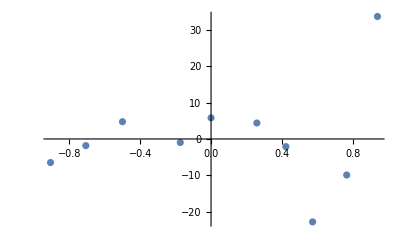

```mathematica
ListPlot[{Cos[#[[1]]Degree],#[[2]]-a1 f1[Cos[#[[1]] Degree]]-a2 f2[Cos[#[[1]] Degree]] - a3 f3[Cos[#[[1]] Degree]]}&/@processedData]
```

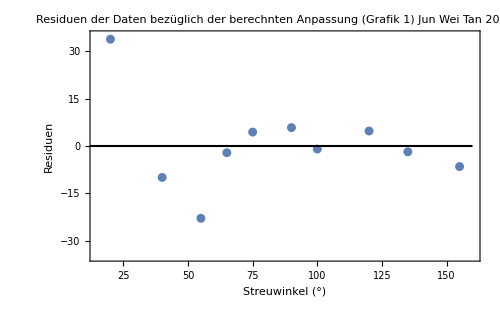

```mathematica
plt2=Show[ListPlot[{#[[1]],#[[2]]-a1 f1[Cos[#[[1]] Degree]]-a2 f2[Cos[#[[1]] Degree]] - a3 f3[Cos[#[[1]] Degree]]}&/@processedData,Frame->True,PlotRange->{{15,160},{-35,35}},Axes->False,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[15,Black,Opacity[1],FontOpacity[1]],LabelStyle->Directive[Black,15,NumberPoint->","],FrameLabel->{"Streuwinkel (°)","Residuen"},PlotLabel->"Residuen der Daten bezüglich\nder berechnten Anpassung (Grafik 1)\n Jun Wei Tan 20.06.24"],Graphics[{Thickness[0.003],Line[{{0,0},{160,0}}]}]]
```

```mathematica
Export[NotebookDirectory[]<>"plt2.pdf",plt2,Background->None];
```

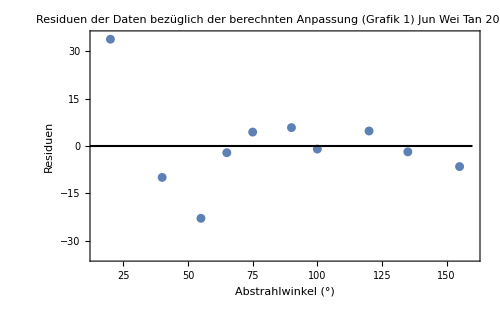

```mathematica
Show[ListPlot[{#[[1]],#[[2]]-theory[#[[1]]]}&/@processedData,Frame->True,PlotRange->{{15,160},{-35,35}},Axes->False,ImageSize->500,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[15,Black,Opacity[1],FontOpacity[1]],LabelStyle->Directive[Black,15,NumberPoint->","],FrameLabel->{"Abstrahlwinkel (°)","Residuen"},PlotLabel->"Residuen der Daten bezüglich\nder berechnten Anpassung (Grafik 1)\n Jun Wei Tan 20.06.24"],Graphics[{Thickness[0.003],Line[{{0,0},{160,0}}]}]]
```

```mathematica
((#1⟦2⟧-theory[#1⟦1⟧])/1&)/@processedData
```

{-6.50526,-1.83838,4.74858,-0.967623,5.81397,4.40359,-2.12052,-22.8642,-9.93189,33.7726}

```mathematica
((#1⟦2⟧-theory[#1⟦1⟧])^2/theory[#1⟦1⟧]&)/@processedData
```

{0.234444,0.0264369,0.261434,0.0195193,0.820722,0.399034,0.0701274,6.08835,0.795941,6.78003}

```mathematica
χ2=Total[((#1⟦2⟧-theory[#1⟦1⟧])^2/theory[#1⟦1⟧]&)/@processedData]
```

15.496

```mathematica
Length[processedData]
```

10

```mathematica
1-CDF[ChiSquareDistribution[6]][7.92488]
```

0.243659

```mathematica
1-CDF[ChiSquareDistribution[7]][χ2]
```

0.0301413